```mathematica
Event Rates
```

```mathematica
opts1={Frame-> True,
FrameLabel->{{"Events/GeV"," "},{"Energy (GeV)", "ν_μ dis. Δm^2=60 Sin^2 2θ_μμ = 0.03"}},
Axes-> False,
(*FrameTicks->{Sort[Flatten[{Table[{0.1*i,},{i,-10,10}],Table[{i-1,ToString[i-1]},{i,0,2,0.2}]},1]],Automatic(*Sort[Flatten[{Table[{5*i,},{i,1,32}],Table[{20*(i-1),ToString[20*(i-1)]},{i,1,7}]},1]]*)},*)
Joined-> True,
InterpolationOrder-> 0,
ImageSize->600,
PlotRange->{{0.2,3},{0,Automatic}},
FrameStyle-> Thick,FrameTicksStyle->Thick, LabelStyle-> (FontSize-> 15)
};
opts2={Frame-> True,
FrameLabel->{{"Events/GeV"," "},{"Energy (GeV)", "LED ν_μ Disappearance"}},
Axes-> False,
(*FrameTicks->{Sort[Flatten[{Table[{0.1*i,},{i,-10,10}],Table[{i-1,ToString[i-1]},{i,0,2,0.2}]},1]],Automatic(*Sort[Flatten[{Table[{5*i,},{i,1,32}],Table[{20*(i-1),ToString[20*(i-1)]},{i,1,7}]},1]]*)},*)
Joined-> True,
InterpolationOrder-> 0,
ImageSize->600,
PlotRange->{{0.2,3},{0,Automatic}},
FrameStyle-> Thick,FrameTicksStyle->Thick, LabelStyle-> (FontSize-> 15)
};
```

```mathematica
optsA={PlotStyle->{Black},Joined-> True,
InterpolationOrder-> 0};
optsB={PlotStyle->{Blue},Joined-> True,
InterpolationOrder-> 0};
optsC={PlotStyle->{Red},Joined-> True,
InterpolationOrder-> 0};
```

```mathematica
NMinimize[Sum[((1+a)*Rate[[i,3]]-Rater[[i,3]]-b*n*10*√Rater[[i,3]])^2/Rater[[i,3]]+((1+a)Ratea[[i,3]]-Ratear[[i,3]]-b*n*√Ratear[[i,3]])^2/Ratear[[i,3]],{i,1,Length[Rate]}]/.n-> 100+(a/0.1)^2+(b)^2,{a,b}]
```

{4.96081,{a→0.0163743,b→-0.000109704}}

```mathematica
{0.0184107,0.0207715,0.0171022,0.0161499,0.0140791,0.0128707,0.0117518,0.0116239,0.0120294,0.0153561,0.0476486}*2.4
```

{0.0441857,0.0498516,0.0410453,0.0387598,0.0337898,0.0308897,0.0282043,0.0278974,0.0288706,0.0368546,0.114357}

### Muons

#### Signal (oscillation on)

```mathematica
Rate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/ev-mm-IC.dat","Data"];
binsμ=Flatten[Append[{0.0},Table[0.2+Sum[Rate[[i,2]],{i,1,x}],{x,1,Length[Rate]}]],1];
tab1=Table[{Rate[[i,1]],(Rate[[i,3]]/Rate[[i,2]])},{i,1,Length[Rate]}];
tab2=Append[Table[{binsμ[[i]],(Rate[[i,3]]/Rate[[i,2]])},{i,1,Length[Rate]}],{binsμ[[Length[binsμ]]],Rate[[Length[Rate],3]]}];(*Junta bin e rates. Repete o último bin pra poder criar os histogramas*)
```

#### No oscillation

```mathematica
Ratea=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/ev-mm-MI.dat","Data"];
(*Usa o mesmo bin da Rate por se tratar do mesmo canal*)
tab1a = Table[{Ratea[[i,1]],(Ratea[[i,3]]/Ratea[[i,2]])},{i,1,Length[Ratea]}];
tab2a= Append[Table[{binsμ[[i]],(Ratea[[i,3]]/Ratea[[i,2]])},{i,1,Length[Ratea]}],{binsμ[[Length[binsμ]]],Rate[[Length[Ratea],3]]}];              (*Junta bin e rates. Repete o último bin pra poder criar os histogramas*)
```

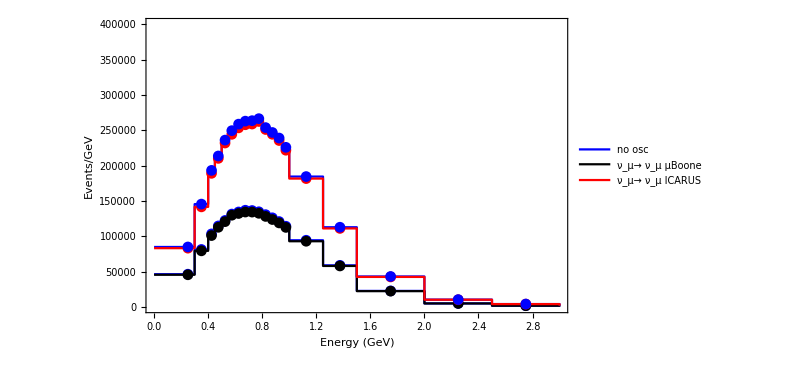

```mathematica
Show[ListPlot@@Flatten[{{tab2a1},opts1,optsB,PlotLegends->{"no osc"}},1],ListPlot[tab1a1,PlotStyle->Blue],ListPlot@@Flatten[{{tab21},opts2,optsB},1],ListPlot@@Flatten[{{tab2a},opts1,optsA,PlotLegends->{"ν_μ→ ν_μ μBoone"}},1],ListPlot[tab1a,PlotStyle->Black],ListPlot@@Flatten[{{tab2},opts2,optsC,PlotLegends->{"ν_μ→ ν_μ ICARUS"}},1],ListPlot[tab1,PlotStyle->Red],ListPlot[tab11,PlotStyle->Blue],PlotRange->{{0,3},{0,4*10^5}}]
```

```mathematica
Export["/home/gstenico/Desktop/nu-LED-2/mm-IC-MI.pdf",Out[320]];
```

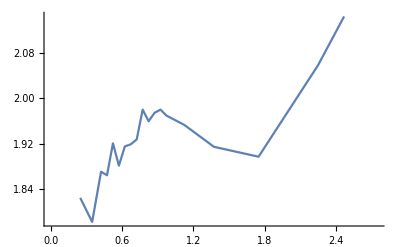

```mathematica
ListPlot[Table[{tab1[[i,1]],tab1[[i,2]]/tab1a[[i,2]]},{i,1,Length[tab1a]}],Joined-> True]
```

### Electrons

#### Signal

```mathematica
Rateb=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/ev-me-ic2.dat","Data"]; (*Contem info de sinal e background*)
binse=Flatten[Append[{0.0},Table[0.2+Sum[Rateb[[i,2]],{i,1,x}],{x,1,Length[Rateb]}]],1];
tab1b=Table[{Rateb[[i,1]],(Rateb[[i,3]]/Rateb[[i,2]]) + (Rateb[[i,4]]/Rateb[[i,2]])},{i,1,Length[Rateb]}]; (*Pontos: sinal em cima do background*)
tab2b=Append[Table[{binse[[i]],(Rateb[[i,3]]/Rateb[[i,2]]) + (Rateb[[i,4]]/Rateb[[i,2]])},{i,1,Length[Rateb]}],{binse[[Length[binse]]],Rateb[[Length[Rateb],3]]}];
(*Junta bin e rates. Repete o último bin pra poder criar os histogramas*)
```

#### Background

```mathematica
tab3b=Table[{Rateb[[i,1]],(Rateb[[i,4]]/Rateb[[i,2]])},{i,1,Length[Rateb]}];
tab4b=Append[Table[{binse[[i]],(Rateb[[i,4]]/Rateb[[i,2]])},{i,1,Length[Rateb]}],{binse[[Length[binse]]],Rateb[[Length[Rateb],3]]}];
(*Junta bin e rates. Repete o último bin pra poder criar os histogramas*)
```

```mathematica
Show[ListPlot@@Flatten[{{tab4b},opts2,optsA,PlotLegends->{"BG"}},1],ListPlot[tab3b,PlotStyle->Black],ListPlot@@Flatten[{{tab2b },opts,optsC,PlotLegends->{"Signal ν_μ→ ν_e  m = 1 eV^2, R= 1 eV^-2))"}},1],ListPlot[tab1b,PlotStyle->Red],PlotRange->{{0,3},{0,3000}}]
```

```mathematica
Rateteste=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/ev-me-ic.dat","Data"];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

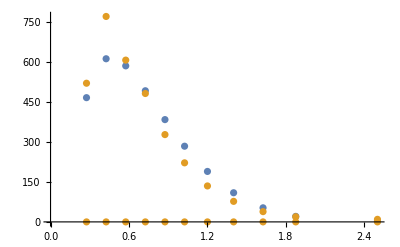

```mathematica
tab1b=Table[{Rateb[[i,1]],(Rateb[[i,3]]/Rateb[[i,2]]) },{i,1,Length[Rateb]}];
tab=Table[{Rateteste[[i,1]],(Rateteste[[i,3]]/Rateteste[[i,2]]) },{i,1,Length[Rateteste]}];
ListPlot[{tab1b,tab}]
```